# Electronic States of the O_2 Diatomic Molecule (groundstate^3 Σ_g symmetry)

```mathematica
SetDirectory[NotebookDirectory[]];
<<../fermifab.m;
<<diatomic_base.m;
fermifabML=Install["../mlink/fermifabML/Windows-x86-64/fermifabML"];
```

```mathematica
<<PhysicalConstants`
```

```mathematica
(* experimental bond length of Subscript[O, 2], in atomic units *)
Subscript[R, O2]=121 10^-12 Meter/BohrRadius
```

2.28657

```mathematica
(* nuclear charge of an oxygen atom *)
Subscript[Z, O]=8;
```

```mathematica
(* quantum numbers *)
Subscript[m, l]=0;
Subscript[s, s]=1;
Subscript[m, s]=1;
```

```mathematica
(* load precomputed integral tables *)
<<diatomic_coulomb_m0_zseries.m;
<<diatomic_coulomb_m1_zseries.m;
<<diatomic_coulomb_m2_zseries.m;
```

```mathematica
SymIntRule[ri_]:=Rule[First[ri],{First[ri],Outer[#+Transpose[#]&,Last[ri],2]}]
```

```mathematica
radinttables={SymIntRule/@radialIntM0TauZSeries,SymIntRule/@radialIntM1TauZSeries,SymIntRule/@radialIntM2TauZSeries};
```

```mathematica
paraInfo=ParaInfo[0(*homonuclear*)]⟦1;;10⟧;
```

```mathematica
QuantNumbersToString[#⟦1;;3⟧]&/@paraInfo
```

{1sσ,1pσ,2sσ,2pσ,1dσ,1p(+π),1p(-π),1d(+π),1d(-π),1fσ}

## Calculate simultaneous LS eigenspaces

```mathematica
diatomicQuantLz=#⟦3⟧&/@paraInfo
```

{0,0,0,0,0,1,-1,1,-1,0}

```mathematica
diatomicParitySpatial=(-1)^(#⟦2⟧)&/@paraInfo
```

{1,-1,1,-1,1,-1,-1,1,1,-1}

```mathematica
diorbnames=Flatten[Outer[#1<>#2&,QuantNumbersToString[#⟦1;;3⟧]&/@paraInfo,{"↑","↓"}]]
Length[diorbnames]
```

{1sσ↑,1sσ↓,1pσ↑,1pσ↓,2sσ↑,2sσ↓,2pσ↑,2pσ↓,1dσ↑,1dσ↓,1p(+π)↑,1p(+π)↓,1p(-π)↑,1p(-π)↓,1d(+π)↑,1d(+π)↓,1d(-π)↑,1d(-π)↓,1fσ↑,1fσ↓}

20

```mathematica
DiatomicAngularMomentumZ[]:=KroneckerProduct[SparseArray[DiagonalMatrix[diatomicQuantLz⟦3;;-1⟧]],IdentityMatrix[2]]
```

```mathematica
DiatomicSpinUp[length_]:=KroneckerProduct[SparseArray[IdentityMatrix[length/2]],{{0,1},{0,0}}]
DiatomicSpinDown[length_]:=KroneckerProduct[SparseArray[IdentityMatrix[length/2]],{{0,0},{1,0}}]
DiatomicSpinZ[length_]:=KroneckerProduct[SparseArray[IdentityMatrix[length/2]],{{1/2,0},{0,-1/2}}]
DiatomicSpin[length_]:=Module[{Su=DiatomicSpinUp[length],Sd=DiatomicSpinDown[length],Sz=DiatomicSpinZ[length]},{(Su+Sd)/2,-ⅈ(Su-Sd)/2,Sz}]
```

```mathematica
DiatomicParity[]:=Flatten[KroneckerProduct[diatomicParitySpatial⟦3;;-1⟧,{1,1}]]
```

```mathematica
(* calculate angular momentum and spin operators *)
diLz=PurgeSparseArray[p2N[DiatomicAngularMomentumZ[],16,1,12]];
diS=PurgeSparseArray[p2N[#,16,1,12]]&/@DiatomicSpin[16];
diSS=PurgeSparseArray[Total[#.#&/@diS]]
```

SparseArray[<5488>,{1820,1820}]

```mathematica
(* select even and odd parity states *)
Times@@(DiatomicParity[]⟦FermiToCoords[#]⟧)&/@FermiMap[16,12];
{peven,podd}={Flatten[Position[%,1]],Flatten[Position[%,-1]]};
Length[peven]
Length[podd]
(*check*)
Length[DeleteDuplicates[Join[peven,podd]]]
```

924

896

1820

```mathematica
(* consistency check: should not overlap *)
diSS⟦Join[peven,podd],Join[peven,podd]⟧
%⟦Length[peven]+1;;-1,1;;Length[peven]⟧//ArrayRules
```

SparseArray[<5488>,{1820,1820}]

{{_,_}→0}

```mathematica
(* simultaneous Subscript[L, z],Subscript[S, z] and S^2 eigenspace with eigenvalues Subscript[m, l]=0, Subscript[m, s]=1 and s=1(1+1) *)
simEven=SparseArray[Orthogonalize[SimNullSpace[diLz⟦peven,peven⟧-Subscript[m, l] SparseArray[IdentityMatrix[Length[peven]]],diS⟦3⟧⟦peven,peven⟧-Subscript[m, s] SparseArray[IdentityMatrix[Length[peven]]],diSS⟦peven,peven⟧-Subscript[s, s](Subscript[s, s]+1)SparseArray[IdentityMatrix[Length[peven]]]]]].SparseArray[IdentityMatrix[Binomial[16,12]]⟦peven,All⟧]
```

SparseArray[<138>,{54,1820}]

```mathematica
(* show entries *)
Union[Last/@ArrayRules[simEven]]
(* check orthonormalization *)
Norm[simEven.Transpose[simEven]-IdentityMatrix[Length[simEven]]]
```

{0,1,√(2/3),-1/(√2),1/(√2),-1/(2 √3),(√3)/2,-1/(√6)}

0

```mathematica
simOdd=SparseArray[Orthogonalize[SimNullSpace[diLz⟦podd,podd⟧-Subscript[m, l] SparseArray[IdentityMatrix[Length[podd]]],diS⟦3⟧⟦podd,podd⟧-Subscript[m, s] SparseArray[IdentityMatrix[Length[podd]]],diSS⟦podd,podd⟧-Subscript[s, s](Subscript[s, s]+1)SparseArray[IdentityMatrix[Length[podd]]]]]].SparseArray[IdentityMatrix[Binomial[16,12]]⟦podd,All⟧]
```

SparseArray[<128>,{56,1820}]

```mathematica
(* show entries *)
Union[Last/@ArrayRules[simOdd]]
(* check orthonormalization *)
Norm[simOdd.Transpose[simOdd]-IdentityMatrix[Length[simOdd]]]
Norm[simOdd.Transpose[simEven]]
```

{0,1,√(2/3),-1/(√2),1/(√2),-1/(2 √3),(√3)/2,-1/(√6)}

0

0

```mathematica
ψFeven=InterleaveFermi[#,FermiMap[{4,16},{4,12}]]&/@simEven;
ψFodd=InterleaveFermi[#,FermiMap[{4,16},{4,12}]]&/@simOdd;
```

```mathematica
(* example *)
ψFeven⟦4⟧
FermiToCoords[Last[%⟦1⟧]]
```

{{-1/(√2),785759},{1/(√2),523631}}

{1,2,3,4,5,7,9,11,12,13,14,15,16,17,18,20}

## Calculate reduced 1- and 2-body density matrices

```mathematica
Subscript[ρ1, even]=SparseArray[Outer[SymToSparseArray[RDM[#2,#1,1],IXI,FermiMap[20,1]]&,ψFeven,ψFeven,1]]
Subscript[ρ2, even]=SparseArray[Outer[SymToSparseArray[RDM[#2,#1,2],IXI,FermiMap[20,2]]&,ψFeven,ψFeven,1]]
```

SparseArray[<1758>,{54,54,20,20}]

SparseArray[<25986>,{54,54,190,190}]

```mathematica
(* example *)
Subscript[ρ1, even]⟦1,4⟧//ArrayRules
Subscript[ρ2, even]⟦1,4⟧//ArrayRules
```

{{6,10}→1/(√2),{_,_}→0}

{{5,9}→1/(√2),{23,27}→1/(√2),{40,44}→1/(√2),{56,60}→1/(√2),{85,144}→-1/(√2),{86,102}→-1/(√2),{88,125}→-1/(√2),{90,136}→1/(√2),{91,137}→1/(√2),{92,138}→1/(√2),{93,139}→1/(√2),{94,140}→1/(√2),{95,141}→1/(√2),{96,142}→1/(√2),{97,143}→1/(√2),{98,144}→1/(√2),{_,_}→0}

### Interleave Fermi states

```mathematica
(* Kronecker products of Fermi maps *)
fm1=FermiMap[20,1];
fmKP1=Flatten[Outer[{##}&,fm1,fm1],1];
```

```mathematica
Subscript[ρ1F, even]=Outer[InterleaveFermi[Flatten[#],fmKP1]&,Subscript[ρ1, even],2];
Dimensions[Subscript[ρ1F, even]]
```

{54,54}

```mathematica
(* Kronecker products of Fermi maps *)
fm2=FermiMap[20,2];
fmKP2=Flatten[Outer[{##}&,fm2,fm2],1];
```

```mathematica
Subscript[ρ2F, even]=Outer[InterleaveFermi[Flatten[#],fmKP2]&,Subscript[ρ2, even],2];
```

```mathematica
Dimensions[Subscript[ρ2F, even]]
```

{54,54}

### Trace out spin

```mathematica
Subscript[ρr1, even]=SparseArray[Outer[SymToSparseArray[SpinTraceSingle[#],SingInt,BosonMap[10,1]]&,Subscript[ρ1F, even],2]]
```

SparseArray[<668>,{54,54,10,10}]

```mathematica
(* example *)
Subscript[ρr1, even]⟦26,26⟧//MatrixForm
```

(2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(* Coulomb operator with symbolic Coulomb integrals *)
Subscript[ρr2, even]=Outer[DiatomicSpinTraceCoulomb,Subscript[ρ2F, even],2];
```

```mathematica
Dimensions[Subscript[ρr2, even]]
```

{54,54}

```mathematica
(* example *)
Subscript[ρr2, even]⟦1,4⟧
```

√2 CoulInt[1,1,3,5]-CoulInt[1,5,3,1]/(√2)+√2 CoulInt[2,2,3,5]-CoulInt[2,5,3,2]/(√2)+CoulInt[3,5,4,4]/(√2)+CoulInt[3,5,5,5]/(√2)+√2 CoulInt[3,5,6,6]+√2 CoulInt[3,5,7,7]+√2 CoulInt[3,5,8,8]+√2 CoulInt[3,5,9,9]+CoulInt[3,5,10,10]/(√2)-CoulInt[3,6,6,5]/(√2)-CoulInt[3,7,7,5]/(√2)-CoulInt[3,8,8,5]/(√2)-CoulInt[3,9,9,5]/(√2)+CoulInt[3,10,10,5]/(√2)

```mathematica
(* enumerate  all required Coulomb integrals *)
clist={};Subscript[ρr2, even]/.CoulInt[a_,b_,c_,d_]:>{clist=Union[clist,{{a,b,c,d}}];0};
Length[clist]
```

264

```mathematica
(* consistency check *)
Norm[Outer[((DiatomicSpinTraceCoulomb[#]/.CoulInt[a_,b_,c_,d_]:>CoulInt[CoordsToBoson[{a,b}],CoordsToBoson[{c,d}]])-SpinTraceCoulomb[#])/.CoulInt[a_,b_]:>CoulInt[b,a]/;b<a&,Subscript[ρ2F, even],2]]
```

0

```mathematica
(* example *)
DiatomicSpinTraceCoulomb[Subscript[ρ2F, even]⟦1,2⟧]
DiatomicSpinTraceCoulomb[Subscript[ρ2F, even]⟦2,1⟧]
```

CoulInt[4,6,10,7]-CoulInt[4,7,10,6]

CoulInt[4,6,10,7]-CoulInt[6,10,7,4]

```mathematica
(* all unique Coulomb integrals after symmetry reduction *)
SparseArray[DeleteDuplicates[Select[Flatten[Table[CoulombSymmetry[a,b,c,d],{a,10},{b,10},{c,10},{d,10}]],#=!=0&]]/.CoulInt[a_,b_,c_,d_]:>Rule[{a,b,c,d},1],{10,10,10,10}]
```

SparseArray[<1126>,{10,10,10,10}]

## Calculate energies

```mathematica
(* example *)
(*Timing[couleval=EvaluateCoulombIntegrals[{2 Subscript[Z, O] Subscript[R, O2],0},Subscript[R, O2],orbParams,clist,radinttables]]
Subscript[ρr2, even]⟦1,2⟧
%/.CoulInt[a_,b_,c_,d_]:>couleval⟦a,b,c,d⟧*)
```

```mathematica
(* dependence on R *)
Rlist=Subscript[R, O2]+Range[-0.5,0.5,0.1]
```

{1.78657,1.88657,1.98657,2.08657,2.18657,2.28657,2.38657,2.48657,2.58657,2.68657,2.78657}

```mathematica
orbParamsList={#,OrbitalParameters[{2 Subscript[Z, O]#,0},paraInfo]}&/@Rlist;
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 20. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
Vee=(Print["R: ",First[#]];Module[{couleval=EvaluateCoulombIntegrals[First[#],Last[#],clist,radinttables]},Subscript[ρr2, even]/.{CoulInt[a_,b_,c_,d_]:>couleval⟦a,b,c,d⟧}])&/@orbParamsList;
```

R: 1.78657

R: 1.88657

R: 1.98657

R: 2.08657

R: 2.18657

R: 2.28657

R: 2.38657

R: 2.48657

R: 2.58657

R: 2.68657

R: 2.78657

```mathematica
Dimensions[Vee]
```

{11,54,54}

```mathematica
singleEnergy=EnergySingle[Subscript[Z, O],{2 Subscript[Z, O] First[#],0},Last[#],Subscript[ρr1, even]]&/@orbParamsList;
```

```mathematica
(* Coulomb repulsion of the nuclei *)
{#,Subscript[Z, O]^2/#}&/@Rlist
Vnn=Subscript[Z, O]^2/# IdentityMatrix[Length[Subscript[ρr1, even]]]&/@Rlist;
```

{{1.78657,35.8229},{1.88657,33.924},{1.98657,32.2164},{2.08657,30.6724},{2.18657,29.2696},{2.28657,27.9895},{2.38657,26.8167},{2.48657,25.7383},{2.58657,24.7432},{2.68657,23.8222},{2.78657,22.9673}}

```mathematica
minEnergyR=Transpose[{Rlist,Min[Eigenvalues[#]]&/@(singleEnergy+Vee+Vnn)}]
```

{{1.78657,-133.},{1.88657,-133.292},{1.98657,-133.484},{2.08657,-133.6},{2.18657,-133.663},{2.28657,-133.687},{2.38657,-133.685},{2.48657,-133.666},{2.58657,-133.64},{2.68657,-133.612},{2.78657,-133.587}}

```mathematica
interpolEnergyR=Interpolation[minEnergyR]
```

InterpolatingFunction[{{1.78657,2.78657}},<>]

```mathematica
(* calculated minimum energy and bond length *)
FindMinimum[interpolEnergyR[R],{R,2.2}]
Emin={R/.Last[%],First[%]}
```

{-133.689,{R→2.32468}}

{2.32468,-133.689}

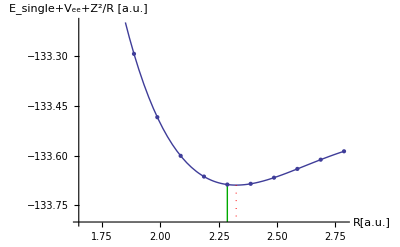

```mathematica
Show[Plot[interpolEnergyR[R],{R,First[Rlist],Last[Rlist]},AxesLabel->{"R[a.u.]","E_single+V_ee+Z^2/R [a.u.]"},AxesOrigin->{1.65,-133.8}],ListPlot[minEnergyR],Graphics[{Darker[Green],Line[{{Subscript[R, O2],-133.8},minEnergyR⟦6⟧}]}],Graphics[{Dotted,Red,Line[{Emin,{First[Emin],-133.8}}]}]]
```

```mathematica
(* minimum energy at experimental bond length *)
minEnergyR⟦6⟧
```

{2.28657,-133.687}

```mathematica
(* smallest eigenvalues at experimental bond length *)
Eigenvalues[singleEnergy⟦6⟧+Vee⟦6⟧+Vnn⟦6⟧]⟦1;;6⟧
(* eigenvalue gaps *)
Differences[%]
```

{-133.687,-133.162,-132.975,-132.887,-132.618,-132.292}

{0.524743,0.187415,0.0876203,0.269308,0.325477}

### Bond dissociation energy

```mathematica
2(-66.7048)
%-Last[Emin]
```

-133.41

0.278971

```mathematica
(* 2 h c Ry *)
2PlanckConstant SpeedOfLight RydbergConstant/(ElectronCharge Volt)
eVToAU=First[%]
```

(27.2114 Joule)/(Coulomb Volt)

27.2114

```mathematica
(* experimental bond dissociation energy of Subscript[O, 2]: 5.114±0.002 eV ("The Dissociation Energy of Oxygen" by P.Brixt and G.Herzberg *)
bondDissEnergyO2=5.114;
```

```mathematica
(* convert to a.u. *)
bondDissEnergyO2/eVToAU
```

0.187936

```mathematica
(* convert to wavelength [m] *)
(PlanckConstant SpeedOfLight)/(bondDissEnergyO2 ElectronCharge)
```

(2.42441×10^-7 Joule Meter)/Coulomb